```mathematica
numberOfTrials = 0; 
probability = 1;
scorePerThrow = 50; (* this defines the number of levels we have*) 
results = List[];
iterator = 0; 
innerIter = 0; 
origBaseScore = 40000; 
lowerScore = 38000;
upperScore = 42000; 
origLowerScore = lowerScore;
origUpperScore = upperScore; 
countInner = 100; 
countOuter = 400;

While [iterator < countOuter, 
runningProbability = 0; 
If [iterator < countOuter/2,
	lowerScore = lowerScore  + 10,(* the +10 controls the increments in the score *) 
	upperScore = upperScore - 10;
	lowerScore = origLowerScore ];
While [ innerIter < countInner,
	runningScore = origBaseScore;
	While [ runningScore >  lowerScore∧ runningScore<  upperScore,
			If [ RandomInteger[1] == 0,
				runningScore = runningScore + scorePerThrow,
				runningScore  = runningScore - scorePerThrow
			   ];
			probability = probability * 0.5; 
		];
	runningProbability = runningProbability + probability; 

	probability = 1; 
	innerIter++;
	];
innerIter = 0; 
totalProbability = runningProbability/countInner; 
runningProbability = 0; 
If [runningScore ≤   origLowerScore ∨ runningScore ≥   origUpperScore, 
	totalProbability  = 0];
	AppendTo[results, {runningScore,totalProbability}];

iterator++; 
]
results
```

{{42000,0},{38000,0},{42000,0},{42000,0},{42000,0},{42000,0},{38050,1.74073×10^-79},{38050,1.18811×10^-68},{38050,5.34553×10^-53},{42000,0},{42000,0},{42000,0},{42000,0},{42000,0},{42000,0},{42000,0},{38150,7.69738×10^-73},{38150,8.35239×10^-55},{42000,0},{42000,0},{38200,1.04405×10^-55},{38200,1.14794×10^-43},{42000,0},{38200,4.48422×10^-46},{38250,2.37419×10^-68},{38250,8.96831×10^-46},{38250,2.408×10^-37},{38250,1.12104×10^-46},{42000,0},{38300,1.20371×10^-37},{38300,3.00927×10^-38},{38300,1.06911×10^-52},{38300,6.84228×10^-51},{42000,0},{38350,9.18355×10^-43},{38350,6.84228×10^-51},{38350,5.47382×10^-50},{42000,0},{42000,0},{38400,3.51127×10^-53},{42000,0},{38400,1.04405×10^-55},{42000,0},{42000,0},{42000,0},{38450,3.95971×10^-33},{42000,0},{38450,6.01853×10^-38},{38450,5.87277×10^-56},{38500,2.86987×10^-44},{38500,4.93038×10^-34},{38500,7.34684×10^-42},{38500,5.04902×10^-31},{38500,4.70198×10^-40},{38550,4.15206×10^-27},{38550,1.61598×10^-29},{42000,0},{42000,0},{42000,0},{42000,0},{42000,0},{38600,8.67362×10^-21},{38600,5.47382×10^-49},{42000,0},{38650,1.54075×10^-35},{38650,1.13687×10^-15},{38650,3.52057×10^-48},{42000,0},{42000,0},{42000,0},{42000,0},{38700,2.06796×10^-27},{38700,8.88182×10^-18},{38700,4.70198×10^-40},{38750,1.65436×10^-26},{38750,3.85187×10^-36},{38750,9.9917×10^-40},{38750,2.46519×10^-34},{42000,0},{42000,0},{38800,5.29396×10^-25},{38800,5.70755×10^-25},{38800,8.67363×10^-21},{38800,5.55112×10^-19},{38850,4.23516×10^-24},{38850,2.62533×10^-28},{42000,0},{38850,1.11023×10^-18},{38850,1.73515×10^-20},{42000,0},{42000,0},{38900,2.11759×10^-24},{38900,3.46945×10^-20},{42000,0},{38950,2.21867×10^-33},{38950,6.77626×10^-23},{38950,1.09267×10^-21},{42000,0},{42000,0},{39000,2.22045×10^-18},{39000,1.38812×10^-19},{39000,3.77476×10^-17},{42000,0},{39000,5.16988×10^-28},{39050,2.60209×10^-20},{39050,1.11463×10^-18},{42000,0},{39050,1.13687×10^-15},{42000,0},{42000,0},{39100,8.91648×10^-18},{39100,2.64698×10^-24},{39100,3.63798×10^-14},{39100,5.96046×10^-10},{39150,2.22221×10^-17},{39150,1.19333×10^-9},{39150,7.68833×10^-17},{39150,6.93954×10^-20},{39150,2.91253×10^-13},{39200,9.53965×10^-9},{42000,0},{42000,0},{39200,3.81569×10^-8},{39200,1.80499×10^-17},{39250,1.18412×10^-12},{39250,4.76837×10^-9},{39250,1.96114×10^-14},{39250,3.14713×10^-7},{42000,0},{39300,3.74348×10^-11},{42000,0},{42000,0},{39300,1.94717×10^-14},{39300,3.65308×10^-14},{39350,3.054×10^-7},{39350,3.16954×10^-10},{39350,4.76867×10^-9},{39350,7.6592×10^-8},{42000,0},{42000,0},{39400,1.36124×10^-9},{42000,0},{42000,0},{39400,5.70303×10^-14},{39450,7.45389×10^-11},{42000,0},{39450,1.00846×10^-7},{39450,4.88759×10^-6},{39450,3.13116×10^-7},{39500,1.67643×10^-7},{42000,0},{39500,3.24567×10^-6},{39500,1.22407×10^-6},{39500,6.20673×10^-7},{39550,3.29418×10^-7},{39550,0.000012023},{39550,4.90846×10^-6},{39550,6.4857×10^-6},{39550,1.75689×10^-6},{39600,0.0000612693},{39600,5.67453×10^-6},{39600,4.44693×10^-6},{42000,0},{39600,0.0000423547},{39650,0.000112379},{39650,0.000135271},{39650,0.0000260756},{39650,0.000314516},{39650,0.0000324562},{39700,0.000308663},{39700,0.000534898},{39700,0.0000920168},{39700,0.000431209},{39700,0.000309007},{39750,0.00111028},{42000,0},{39750,0.000708473},{39750,0.000859483},{39750,0.00195703},{39800,0.00502173},{42000,0},{39800,0.00810503},{39800,0.00715408},{39800,0.00561694},{39850,0.0124351},{39850,0.025665},{39850,0.0202903},{39850,0.0178429},{39850,0.0210104},{39900,0.0841563},{39900,0.060553},{39900,0.0600826},{39900,0.056141},{39900,0.0716169},{39950,0.2788},{39950,0.314973},{39950,0.221043},{39950,0.292399},{39950,0.253776},{40000,1},{38000,0},{38000,0},{42000,0},{42000,0},{38000,0},{38000,0},{38000,0},{38000,0},{41950,5.22024×10^-56},{38000,0},{38000,0},{41900,3.18618×10^-59},{41900,9.54251×10^-68},{41900,1.06912×10^-52},{41850,5.73972×10^-44},{38000,0},{38000,0},{38000,0},{38000,0},{41800,1.63133×10^-57},{38000,0},{41800,1.14794×10^-43},{41800,5.79563×10^-72},{38000,0},{38000,0},{38000,0},{38000,0},{41750,2.40741×10^-37},{38000,0},{41700,2.86986×10^-44},{38000,0},{41700,3.08168×10^-35},{41700,3.00927×10^-38},{41700,7.34684×10^-42},{41650,8.35239×10^-55},{41650,3.76158×10^-39},{38000,0},{41650,2.8026×10^-47},{38000,0},{38000,0},{41600,1.20371×10^-37},{41600,3.15544×10^-32},{38000,0},{41600,4.93038×10^-34},{38000,0},{38000,0},{38000,0},{41550,4.59177×10^-43},{41550,1.18695×10^-68},{41500,4.81483×10^-37},{38000,0},{41500,1.88079×10^-39},{41500,5.04871×10^-31},{41500,4.48443×10^-46},{38000,0},{41450,5.73972×10^-44},{38000,0},{41450,6.01853×10^-38},{38000,0},{38000,0},{41400,7.88861×10^-33},{41400,1.83671×10^-42},{41400,4.93038×10^-34},{41400,2.86986×10^-44},{41350,1.65436×10^-26},{41350,4.23202×10^-39},{41350,1.03398×10^-27},{38000,0},{41350,2.46523×10^-34},{38000,0},{41300,3.17085×10^-32},{41300,1.26218×10^-31},{41300,4.55641×10^-46},{38000,0},{38000,0},{41250,2.58494×10^-28},{38000,0},{38000,0},{41250,3.85186×10^-36},{41200,2.22045×10^-18},{38000,0},{41200,2.06795×10^-27},{41200,1.2928×10^-28},{41200,1.29247×10^-28},{41150,6.56332×10^-29},{41150,8.47033×10^-23},{41150,4.44089×10^-18},{41150,1.71696×10^-29},{41150,1.60237×10^-32},{41100,5.07829×10^-31},{41100,7.57306×10^-31},{41100,1.35525×10^-22},{41100,3.46945×10^-20},{41100,7.70372×10^-36},{38000,0},{41050,1.77809×10^-17},{41050,6.61906×10^-26},{38000,0},{41050,4.44091×10^-18},{41000,3.72529×10^-11},{41000,2.33058×10^-12},{38000,0},{38000,0},{41000,2.27596×10^-15},{40950,1.81899×10^-14},{40950,6.93974×10^-20},{40950,7.30438×10^-14},{40950,7.10543×10^-17},{40950,1.08421×10^-21},{40900,9.09745×10^-15},{40900,9.09495×10^-15},{40900,5.68434×10^-16},{40900,2.45196×10^-15},{38000,0},{38000,0},{38000,0},{40850,1.16415×10^-12},{40850,1.3932×10^-18},{40850,4.83176×10^-15},{40800,1.47793×10^-13},{40800,1.49057×10^-10},{38000,0},{40800,5.42103×10^-22},{40800,5.82077×10^-13},{40750,7.45422×10^-11},{40750,7.62939×10^-8},{40750,1.81902×10^-14},{40750,1.89186×10^-11},{40750,8.88178×10^-17},{40700,7.34701×10^-14},{40700,4.80562×10^-9},{38000,0},{40700,1.52746×10^-7},{40700,1.4916×10^-10},{40650,1.30177×10^-6},{40650,5.96179×10^-9},{40650,3.06444×10^-7},{40650,5.06639×10^-9},{38000,0},{40600,2.4821×10^-6},{40600,3.28351×10^-9},{40600,1.90772×10^-7},{38000,0},{40600,1.37213×10^-8},{40550,8.44896×10^-9},{40550,1.49991×10^-9},{40550,3.05194×10^-7},{40550,8.14931×10^-8},{40550,2.0303×10^-8},{40500,9.28059×10^-7},{40500,8.21581×10^-7},{38000,0},{38000,0},{40500,2.31909×10^-7},{40450,0.0000393853},{40450,7.1208×10^-6},{38000,0},{40450,1.68998×10^-6},{38000,0},{40400,5.91891×10^-6},{38000,0},{40400,0.0000216712},{40400,0.0000424226},{40400,8.14258×10^-7},{40350,0.000104941},{40350,0.0000302559},{40350,0.000132372},{40350,0.000180856},{40350,0.0000249017},{40300,0.000624798},{40300,0.000300026},{40300,0.000334729},{40300,0.000321632},{40300,0.000304492},{40250,0.00101287},{40250,0.000985178},{40250,0.000840638},{40250,0.00214689},{40250,0.00152659},{40200,0.00537025},{40200,0.00593497},{40200,0.00485853},{40200,0.00455837},{38000,0},{38000,0},{40150,0.0167228},{40150,0.017995},{40150,0.02223},{40150,0.0207867},{40100,0.0757423},{40100,0.0568486},{40100,0.070343},{40100,0.0818692},{40100,0.0677864},{40050,0.223142},{40050,0.267689},{40050,0.282799},{40050,0.285149},{40050,0.298248},{40000,1}}

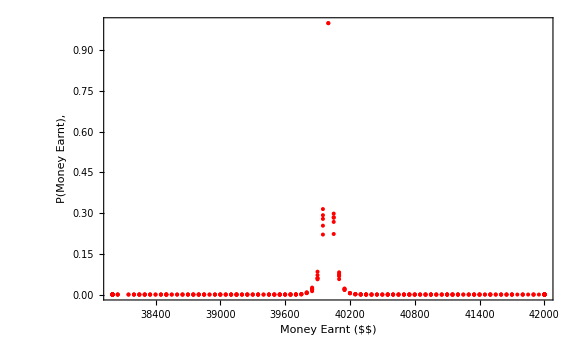

```mathematica
dataPlot = ListPlot[results,PlotRange->All,ImageSize->Large, Joined->False,Frame->True,FrameLabel->{"Money Earnt ($$)","P(Money Earnt),","Conditions= 
origBaseScore = 40000; 
scorePerThrow = 50;
lowerScore = 38000; 
upperScore = 42000; 
countInner = 100; 
countOuter = 400;
P = P * 0.5; 0.9 in all other cases in this window  
lowerScore = lowerScore  + 10;
upperScore = upperScore - 10;",""}, LabelStyle->{FontSize->14, Directive[Bold,Black]}, PlotStyle->{RGBColor[1,0,0],PointSize[0.005]}]
myFit = Fit[results,{0.4^x},x];
fitPlot = Plot[myFit,{x,400,404}];
Show[fitPlot,dataPlot];
```